# Fourier Series

```mathematica
f[x]=∑Subscript[C, n] Cos[n x]+Subscript[S, n] Sin[n x],n≥0
(*or*)
f[x]=∑Subscript[N, n] e^(in x),
where SuperStar[Subscript[N, n]]=Subscript[N, -n]
x∈[-π,+π]
```

```mathematica
(* Remark*)
f[x+2k π]=f[x]
```

```mathematica
Table[Integrate[Cos[n x]Cos[m x],{x,-π,π}],{n,0,10},{m,0,10}]
```

{{2 π,0,0,0,0,0,0,0,0,0,0},{0,π,0,0,0,0,0,0,0,0,0},{0,0,π,0,0,0,0,0,0,0,0},{0,0,0,π,0,0,0,0,0,0,0},{0,0,0,0,π,0,0,0,0,0,0},{0,0,0,0,0,π,0,0,0,0,0},{0,0,0,0,0,0,π,0,0,0,0},{0,0,0,0,0,0,0,π,0,0,0},{0,0,0,0,0,0,0,0,π,0,0},{0,0,0,0,0,0,0,0,0,π,0},{0,0,0,0,0,0,0,0,0,0,π}}

```mathematica
Table[Integrate[Cos[n x]Sin[m x],{x,-π,π}],{n,0,10},{m,0,10}]
```

{{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
Table[Integrate[Sin[n x]Sin[m x],{x,-π,π}],{n,0,10},{m,0,10}]
```

{{0,0,0,0,0,0,0,0,0,0,0},{0,π,0,0,0,0,0,0,0,0,0},{0,0,π,0,0,0,0,0,0,0,0},{0,0,0,π,0,0,0,0,0,0,0},{0,0,0,0,π,0,0,0,0,0,0},{0,0,0,0,0,π,0,0,0,0,0},{0,0,0,0,0,0,π,0,0,0,0},{0,0,0,0,0,0,0,π,0,0,0},{0,0,0,0,0,0,0,0,π,0,0},{0,0,0,0,0,0,0,0,0,π,0},{0,0,0,0,0,0,0,0,0,0,π}}

```mathematica
therefore, we better write as
f[x]=Subscript[A, 0]/(2π)+∑Subscript[C, n] Cos[n x]+Subscript[S, n] Sin[n x],n>0

Subscript[A, 0]=1/π∫_-π^π f[x]ⅆx
Subscript[C, n]=1/π∫_-π^π f[x]Cos[n x]ⅆx
Subscript[S, n]=1/π∫_-π^π f[x]Sin[n x]ⅆx
```

## Example

```mathematica
f=x
```

x

```mathematica
(* Subscript[A, 0]*)
A0=Integrate[f,{x,-π,π}]/π;
(* Subscript[C, n] *)
Cn=Table[Integrate[f Cos[n x],{x,-π,π}],{n,1,20}]/π;
(* Subscript[S, n] *)
Sn=Table[Integrate[f Sin[n x],{x,-π,π}],{n,1,20}]/π;
```

```mathematica
ff[m_]:=A0/2+Sum[Cn[[n]] Cos[n x]+Sn[[n]]Sin[n x],{n,1,m}]
```

```mathematica
ff[8]
```

2 Sin[x]-Sin[2 x]+2/3 Sin[3 x]-1/2 Sin[4 x]+2/5 Sin[5 x]-1/3 Sin[6 x]+2/7 Sin[7 x]-1/4 Sin[8 x]

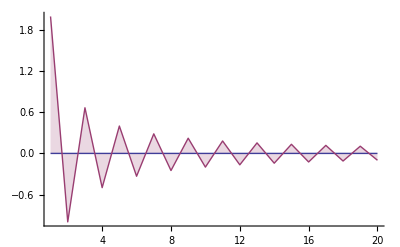

```mathematica
ListLinePlot[{Cn,Sn},Filling->Axis,PlotRange->All]
```

```mathematica
Manipulate[Plot[{ff[m],f},{x,-π-0.5,π+0.5}],{m,1,20,1}]
```

## Example 2

```mathematica
g=UnitStep[x]
```

UnitStep[x]

```mathematica
(* Subscript[A, 0]*)
A0=Integrate[g,{x,-π,π}]/π;
(* Subscript[C, n] *)
Cn=Table[Integrate[g Cos[n x],{x,-π,π}],{n,1,20}]/π;
(* Subscript[S, n] *)
Sn=Table[Integrate[g Sin[n x],{x,-π,π}],{n,1,20}]/π;
```

```mathematica
gf[m_]:=A0/2+Sum[Cn[[n]] Cos[n x]+Sn[[n]]Sin[n x],{n,1,m}]
```

```mathematica
gf[2]
```

1+(2 Sin[x])/π

```mathematica
Manipulate[Plot[{g,gf[m]},{x,-π,π}],{m,1,20,1}]
```

## Complex Fourier Series

```mathematica
f[x]=Subscript[A, 0]/2+∑Subscript[C, n] Cos[n x]+Subscript[S, n] Sin[n x],n>0

x∈[-π,+π]

Subscript[A, 0]=1/π∫_-π^π f[x]ⅆx
Subscript[C, n]=1/π∫_-π^π f[x]Cos[n x]ⅆx
Subscript[S, n]=1/π∫_-π^π f[x]Sin[n x]ⅆx

f[x]=∑Subscript[N, n] e^(in x),where SuperStar[Subscript[N, n]]=Subscript[N, -n]
	=∑(Subscript[N, n]+Subscript[N, -n])Cos[nx]+i(Subscript[N, n]-Subscript[N, -n])Sin[nx]
Subscript[N, n]+Subscript[N, -n]=Subscript[C, n]
Subscript[N, n]-Subscript[N, -n]=-Subscript[iS, n]
Subscript[N, n]=(Subscript[C, n]-Subscript[iS, n])/2
Subscript[N, -n]=(Subscript[C, n]+Subscript[iS, n])/2
```

## Example

```mathematica
k=x;
```

```mathematica
(* Subscript[A, 0]*)
A0=Integrate[f,{x,-π,π}]/π;
(* Nn *)
Nn=Table[Integrate[k Exp[ⅈ n x],{x,-π,π}],{n,1,20}]/π;
kf[m_]:=A0/2+Sum[Re[Nn[[n]]]Cos[n x]+Im[Nn[[n]]]Sin[n x],{n,1,m}]
ListPlot[{Re[Nn],Im[Nn]},Filling->Axis,Joined-> True,PlotRange->All]
Manipulate[Plot[{kf[m],k},{x,-π-0.5,π+0.5}],{m,1,20,1}]
```

-Graphics-